```mathematica
speck = FullSimplify[Solve[VarZ==(1-s)/(n-1)*A + s*B - ((1-s)/(n-1)*c + s*d)^2,s]]
```

{{s→1/(2 (c+d-d n)^2)(-1+n)^2 (B+(A-A n+2 c (c+d-d n))/(-1+n)^2-√(1/(-1+n)^2(A^2+2 A (B-2 d (c+d)-B n+2 d^2 n)+B (B (-1+n)^2+4 c (c+d-d n))-4 (c+d-d n)^2 VarZ)))},{s→1/(2 (c+d-d n)^2)(-1+n)^2 (B+(A-A n+2 c (c+d-d n))/(-1+n)^2+√(1/(-1+n)^2(A^2+2 A (B-2 d (c+d)-B n+2 d^2 n)+B (B (-1+n)^2+4 c (c+d-d n))-4 (c+d-d n)^2 VarZ)))}}

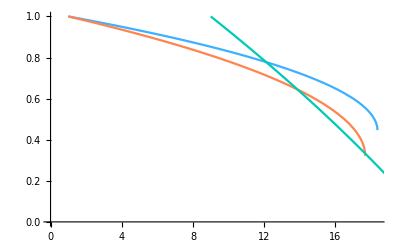

```mathematica
mu = {-14,-5,-8};
sig = {1,1,3};
nprey = Length[mu];
Show[Table[Plot[(s/.speck[[2]])/.{A->Sum[(sig[[i]]^2+mu[[i]]^2)Boole[i≠k],{i,1,nprey}],B->(sig[[k]]^2+mu[[k]]^2),c->Sum[(mu[[i]])Boole[i≠k],{i,1,nprey}],d->mu[[k]],n->nprey},{VarZ,1,20},PlotRange->{0,1},PlotStyle->ColorData[96,k]],{k,{1,2,3}}]
]
```